```mathematica
Table[
With[{colors=4,k=4},

{StirlingS2[n,4],Sum[( StirlingS1[colors,colors-i]StirlingS2[n-i,n-k]),{i,0,colors-1}]}
],
{n,5,10}
]
```

{{10,0},{65,0},{350,0},{1701,256},{7770,2101},{34105,9751}}

```mathematica
Table[Table[StirlingS1[n,k],{k,1,n}],{n,1,10}]//TableForm
```

1 |  |  |  |  |  |  |  |  | 
-1 | 1 |  |  |  |  |  |  |  | 
2 | -3 | 1 |  |  |  |  |  |  | 
-6 | 11 | -6 | 1 |  |  |  |  |  | 
24 | -50 | 35 | -10 | 1 |  |  |  |  | 
-120 | 274 | -225 | 85 | -15 | 1 |  |  |  | 
720 | -1764 | 1624 | -735 | 175 | -21 | 1 |  |  | 
-5040 | 13068 | -13132 | 6769 | -1960 | 322 | -28 | 1 |  | 
40320 | -109584 | 118124 | -67284 | 22449 | -4536 | 546 | -36 | 1 | 
-362880 | 1026576 | -1172700 | 723680 | -269325 | 63273 | -9450 | 870 | -45 | 1

```mathematica
-10StirlingS2[10,5]
```

-425250

```mathematica
Table[
{n->StirlingS2[n,4],3*StirlingS2[n-1,4]-StirlingS2[n-2,4]}
,
{n,4,10}
]
```

{{4→1,0},{5→10,3},{6→65,29},{7→350,185},{8→1701,985},{9→7770,4753},{10→34105,21609}}

```mathematica
With[
{colors=3},
Table[
{n->StirlingS2[n,colors],6*StirlingS2[n-1,colors]-3StirlingS2[n-2,colors]+StirlingS2[n-3,colors]}
,
{n,4,10}
]
]
```

{{4→6,6},{5→25,33},{6→90,133},{7→301,471},{8→966,1561},{9→3025,4983},{10→9330,15553}}

```mathematica
Map[7-StringCount[SymbolName[#],"x"]&,ListofVars[allGraphs6[K4Key,"colofour"]]]//Tally
```

{{4,16},{3,9},{2,1}}

```mathematica
TableForm[Table[
max->Sort[Tally[Map[max-StringCount[SymbolName[#],"x"]&,ListofVars[FindFullFormula[VertexAdd[CompleteGraph[3],Range[4,max]]]]]]],
{max,4,10}
]]
```

4→{{1,1},{2,3}}
5→{{1,1},{2,7},{3,9}}
6→{{1,1},{2,12},{3,37},{4,27}}
7→{{1,1},{2,18},{3,97},{4,175},{5,81}}
8→{{1,1},{2,25},{3,205},{4,660},{5,781},{6,243}}
9→{{1,1},{2,33},{3,380},{4,1890},{5,4081},{6,3367},{7,729}}
10→{{1,1},{2,42},{3,644},{4,4550},{5,15421},{6,23772},{7,14197},{8,2187}}

```mathematica
TableForm[Table[
max->Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[FindFullFormula[VertexAdd[CompleteGraph[4],Range[5,max]]]]]]],
{max,4,10}
]]
```

4→{{4,1}}
5→{{4,4},{5,1}}
6→{{4,16},{5,9},{6,1}}
7→{{4,64},{5,61},{6,15},{7,1}}
8→{{4,256},{5,369},{6,151},{7,22},{8,1}}
9→{{4,1024},{5,2101},{6,1275},{7,305},{8,30},{9,1}}
10→{{4,4096},{5,11529},{6,9751},{7,3410},{8,545},{9,39},{10,1}}

```mathematica
TableForm[Table[
max->Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[FindFullFormula[VertexAdd[CompleteGraph[3],Range[4,max]]]]]]],
{max,3,10}
]]
```

3→{{3,1}}
4→{{3,3},{4,1}}
5→{{3,9},{4,7},{5,1}}
6→{{3,27},{4,37},{5,12},{6,1}}
7→{{3,81},{4,175},{5,97},{6,18},{7,1}}
8→{{3,243},{4,781},{5,660},{6,205},{7,25},{8,1}}
9→{{3,729},{4,3367},{5,4081},{6,1890},{7,380},{8,33},{9,1}}
10→{{3,2187},{4,14197},{5,23772},{6,15421},{7,4550},{8,644},{9,42},{10,1}}

```mathematica
Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[3],Range[4,5]]]],StringCount[SymbolName[#],"x"]+1==3&]]
```

9

```mathematica
Count[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[FindFullFormula[VertexAdd[CompleteGraph[3],Range[4,max]]]]]
```

```mathematica
With[
{colors=3},
TableForm[Table[
With[{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors],Range[colors+1,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},
{n,StirlingS2[n,colors],StirlingS2[n-1,colors],StirlingS2[n-2,colors],3StirlingS2[n-1,colors]-2StirlingS2[n-2,colors],good, StirlingS2[n,colors]-good
}
],{n,colors,10}
], TableHeadings->{None, {"n","n3","n-1,3","n-2,3","formula","good","bad"}}]
]
```

n | n3 | n-1,3 | n-2,3 | formula | good | bad
3 | 1 | 0 | 0 | 0 | 1 | 0
4 | 6 | 1 | 0 | 3 | 3 | 3
5 | 25 | 6 | 1 | 16 | 9 | 16
6 | 90 | 25 | 6 | 63 | 27 | 63
7 | 301 | 90 | 25 | 220 | 81 | 220
8 | 966 | 301 | 90 | 723 | 243 | 723
9 | 3025 | 966 | 301 | 2296 | 729 | 2296
10 | 9330 | 3025 | 966 | 7143 | 2187 | 7143

```mathematica
With[
{colors=4},
TableForm[Table[
With[{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors],Range[colors+1,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},
{
n,
a StirlingS2[n-1,colors]-b StirlingS2[n-2,colors]+c StirlingS2[n-3,colors] == StirlingS2[n,colors ]-good,
good,
 StirlingS2[n,colors ]-good
}
],{n,colors,10}
], TableHeadings->{None, {"n","formula","good","bad"}}]
]
```

```mathematica
TableForm[Table[
max->Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[FindFullFormula[VertexAdd[CompleteGraph[5],Range[6,max]]]]]]],
{max,5,10}
]]
```

5→{{5,1}}
6→{{5,5},{6,1}}
7→{{5,25},{6,11},{7,1}}
8→{{5,125},{6,91},{7,18},{8,1}}
9→{{5,625},{6,671},{7,217},{8,26},{9,1}}
10→{{5,3125},{6,4651},{7,2190},{8,425},{9,35},{10,1}}

```mathematica
FactorInteger[369]
```

{{3,2},{41,1}}

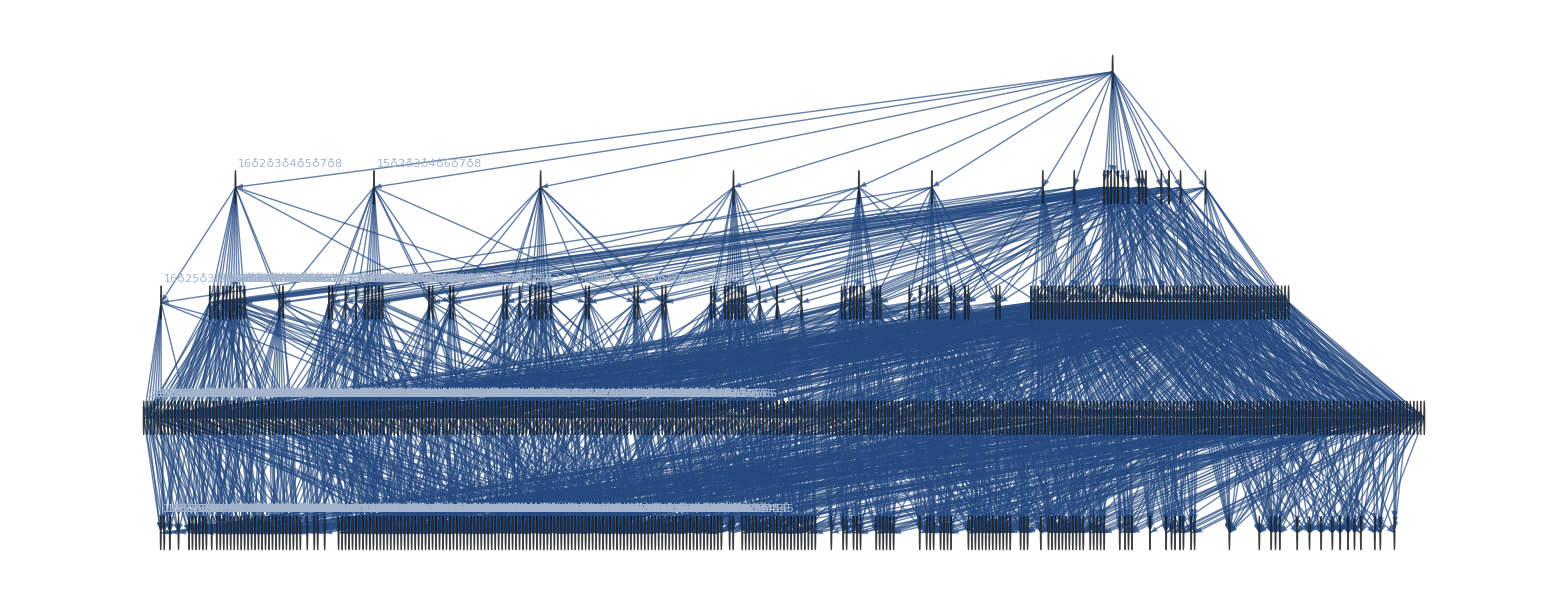

```mathematica
Graph[FormulaGraph[FindFullFormula[VertexAdd[CompleteGraph[4],{5,6,7,8}]]],ImageSize->{2000,400}]
```

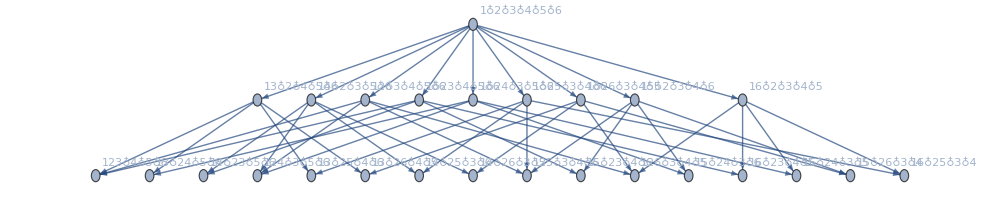

```mathematica
Graph[FormulaGraph[allGraphs6[K4Key,"colofour"]],ImageSize->{1000,200}]
```

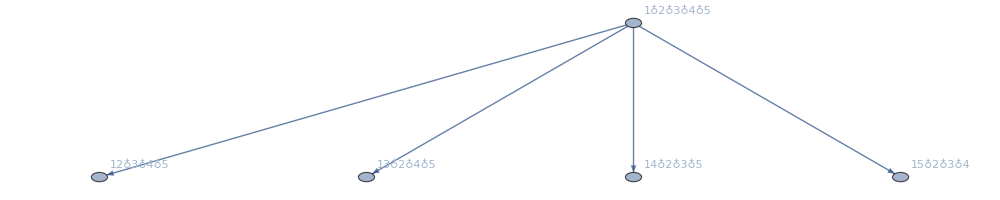

```mathematica
Graph[FormulaGraph[allGraphs5[K4Key,"colofour"]],ImageSize->{1000,200}]
```

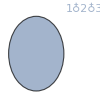

```mathematica
Graph[FormulaGraph[allGraphs4[K4Key,"colofour"]],ImageSize->{100,100}]
```

```mathematica
allGraphs6[K4Key,"colofour"]
```

v123x4x5x6+v124x3x5x6+v125x3x4x6+v126x3x4x5+v12x3x4x5x6+v13x24x5x6+v13x25x4x6+v13x26x4x5+v13x2x4x5x6+v14x23x5x6+v14x25x3x6+v14x26x3x5+v14x2x3x5x6+v15x23x4x6+v15x24x3x6+v15x26x3x4+v15x2x3x4x6+v16x23x4x5+v16x24x3x5+v16x25x3x4+v16x2x3x4x5+v1x23x4x5x6+v1x24x3x5x6+v1x25x3x4x6+v1x26x3x4x5+v1x2x3x4x5x6